## Neural net initilization

```mathematica
ClearAll[tnet]
tnet = Import[File["/Users/mehmetsahin/Downloads/2017-12-27T18-42-44_0_0123_05898_3.71e-3_9.47e-2.wlnet"]]
```

NetChain[<>]

```mathematica
choppedTNet = NetTake[tnet,1]
```

NetChain[<>]

```mathematica
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[1000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
netJoin = NetJoin[choppedTNet,finalLayers]
```

NetChain[<>]

## Functions

```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[rootfolder_,folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],rootfolder,folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName[fileName]]["Zoom"];
```

```mathematica
ClearAll[getGeoRange]
getGeoRange[zoom_,max_] := zoom * max;
```

```mathematica
binaryWrite[expr_]:=binaryWrite[expr,CreateFile[]];
binaryWrite[expr_,file_]:=With[{bytes=BinaryWrite[file,BinarySerialize[expr]]},Close[file];
bytes];
binaryRead[file_]:=BinaryDeserialize[ReadByteArray[file]];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		fileNames
	]
```

```mathematica
filewxfLocation[rootfolder_,folderName_] := 
	FileNameJoin[{NotebookDirectory[],rootfolder,folderName<>".wxf"}]
```

```mathematica
savewxf[file_,filewxfLocation_] := 
	binaryWrite[file,filewxfLocation];
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

Try with city images ranged between  0.2 to 4 miles that were rounded (around 150 training data):

### Get features:

```mathematica
Print["Starting!"];
validFeatures = MapAt[choppedTNet,RandomSample[associateFilesToGeoRange[getFileNames["RoundedCityImages","validation"]]],{All,1}];
Print["First part done!"];
trainFeatures = MapAt[choppedTNet,RandomSample[associateFilesToGeoRange[getFileNames["RoundedCityImages","training"]]],{All,1}];
Print["done! Starting the training"];
```

Starting!

First part done!

done! Starting the training

### Save wfx:

```mathematica
binaryWrite[trainFeatures,FileNameJoin[{NotebookDirectory[],"RoundedCityImages","trainFeatures.wxf"}]];
Print["done"];
binaryWrite[validFeatures,FileNameJoin[{NotebookDirectory[],"RoundedCityImages","validationFeatures.wxf"}]];
```

done

### Try:

```mathematica
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[8000],ElementwiseLayer[Ramp],LinearLayer[1000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
featureTrainedNet = NetTrain[finalLayers,trainFeatures,ValidationSet->validFeatures]
```

NetChain[<>]

```mathematica
lastLayerJoin = NetJoin[choppedTNet,featureTrainedNet]
ClearAll[testData]
testData = RandomSample@associateFilesToGeoRange[getFileNames["RoundedCityImages","testing"]];
```

NetChain[<>]

```mathematica
calculateError[lastLayerJoin,testData]
calculateMeanSq[lastLayerJoin,testData]
```

0.536517

0.0244803

```mathematica
min = 30;
max = 35;
testData[[min;;max]]//Dataset
Map[Import,testData[[min;;max,1]]]
lastLayerJoin[Map[Import,testData[[min;;max,1]]]]
```

Dataset[<>]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.148134,0.555327,0.470304,0.718496,0.457024,0.625795}

city images ranged between  0.2 to 4 miles:

### get features:

```mathematica
Print["Starting!"];
validFeatures = MapAt[choppedTNet,RandomSample[associateFilesToGeoRange[getFileNames["CityImages","validation"]]],{All,1}];
Print["First part done!"];
trainFeatures = MapAt[choppedTNet,RandomSample[associateFilesToGeoRange[getFileNames["CityImages","training"]]],{All,1}];
Print["done! Starting the training"];
```

Starting!

First part done!

done! Starting the training

### Save wxf:

```mathematica
binaryWrite[trainFeatures,FileNameJoin[{NotebookDirectory[],"CityImages","trainFeatures.wxf"}]];
Print["done"];
binaryWrite[validFeatures,FileNameJoin[{NotebookDirectory[],"CityImages","validationFeatures.wxf"}]];
```

### Get back the wxf:

```mathematica
filewxfLocation["CityImages","trainFeatures"]
```

/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/trainFeatures.wxf

```mathematica
ClearAll[validFeatures]
validFeatures = binaryRead[filewxfLocation["CityImages","trainFeatures"]];
```

```mathematica
ClearAll[trainFeatures]
trainFeatures = binaryRead[filewxfLocation["CityImages","trainFeatures"]];
```

### Try on neural nets:

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[8000],ElementwiseLayer[Ramp],LinearLayer[1000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[featureTrainedNet]
featureTrainedNet = NetTrain[finalLayers,trainFeatures,ValidationSet->validFeatures]
```

NetChain[<>]

```mathematica
ClearAll[lastLayerJoin,testData]
lastLayerJoin = NetJoin[choppedTNet,featureTrainedNet]
ClearAll[testData]
testData = RandomSample@associateFilesToGeoRange[getFileNames["CityImages","testing"]];
```

NetChain[<>]

```mathematica
calculateError[lastLayerJoin,testData]
calculateMeanSq[lastLayerJoin,testData]
```

0.51492

0.0174856

```mathematica
min = 35;
max = 40;
testData[[min;;max]]
Map[Import,testData[[min;;max,1]]]
lastLayerJoin[Map[Import,testData[[min;;max,1]]]]
```

{File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECvERt+8C4PUAihWo3xdNXwC1TBFpvb21ytGaAtnU45D9DBA==/ODpBAi1TBFpvb21ytGaAtnU41D8tUwZOdW1iZXJDAg==.png]→0.315946,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECMgbhOXvYPUCxlHYVGdtXwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21ympmZmZmZuT8tUwZOdW1iZXJDBA==.png]→0.1,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECL78b4EJfQECHABv2oz1YwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21yERERERERsT8tUwZOdW1iZXJDBQ==.png]→0.0666667,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECMgbhOXvYPUCxlHYVGdtXwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21yERERERERsT8tUwZOdW1iZXJDAQ==.png]→0.0666667,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwEC7TgTP~P1REAVUz0+nulVwC1TBFpvb21ytHzDFLS65D9DBA==/ODpBAi1TBFpvb21ymvtZxpqjyz8tUwZOdW1iZXJDBA==.png]→0.21593,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECL78b4EJfQECHABv2oz1YwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21yERERERERsT8tUwZOdW1iZXJDAw==.png]→0.0666667}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.283668,0.109172,0.130727,0.120367,0.156968,0.126293}

### Try with different final layer on neural nets:

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{PoolingLayer[4,"Function"->Mean],FlattenLayer[],LinearLayer[3000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[featureTrainedNet]
featureTrainedNet = NetTrain[finalLayers,trainFeatures,ValidationSet->validFeatures]
```

NetChain[<>]

```mathematica
ClearAll[lastLayerJoin,testData]
lastLayerJoin = NetJoin[choppedTNet,featureTrainedNet]
ClearAll[testData]
testData = RandomSample@associateFilesToGeoRange[getFileNames["CityImages","testing"]];
```

NetChain[<>]

```mathematica
calculateError[lastLayerJoin,testData]
calculateMeanSq[lastLayerJoin,testData]
```

0.548165

0.0267579

```mathematica
min = 35;
max = 40;
testData[[min;;max]]
Map[Import,testData[[min;;max,1]]]
lastLayerJoin[Map[Import,testData[[min;;max,1]]]]
```

{File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECvERt+8C4PUAihWo3xdNXwC1TBFpvb21ytGaAtnU45D9DBA==/ODpBAi1TBFpvb21ytGaAtnU41D8tUwZOdW1iZXJDAg==.png]→0.315946,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECMgbhOXvYPUCxlHYVGdtXwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21ympmZmZmZuT8tUwZOdW1iZXJDBA==.png]→0.1,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECL78b4EJfQECHABv2oz1YwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21yERERERERsT8tUwZOdW1iZXJDBQ==.png]→0.0666667,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECMgbhOXvYPUCxlHYVGdtXwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21yERERERERsT8tUwZOdW1iZXJDAQ==.png]→0.0666667,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwEC7TgTP~P1REAVUz0+nulVwC1TBFpvb21ytHzDFLS65D9DBA==/ODpBAi1TBFpvb21ymvtZxpqjyz8tUwZOdW1iZXJDBA==.png]→0.21593,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CityImages/testing/ODpmAnMEUnVsZUECLVMFUG9pbnTBIwECL78b4EJfQECHABv2oz1YwC1TBFpvb21ympmZmZmZyT9DBA==/ODpBAi1TBFpvb21yERERERERsT8tUwZOdW1iZXJDAw==.png]→0.0666667}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.283668,0.109172,0.130727,0.120367,0.156968,0.126293}

Try on smaller images of ranged between 0.2 to 1200 mile

### The neural net was not able to learn after trying feature extractor with 200 training, 40 validation and 10 test images.

```mathematica
trainingData = associateFilesToGeoRange[getFileNames["training"]];
validationData = associateFilesToGeoRange[getFileNames["validation"]];
```

```mathematica
testData = associateFilesToGeoRange[getFileNames["testing"]];
```

```mathematica
trainingDataGeo = MapAt[getGeoRange,trainingData,{All,2}];
validationDataGeo = MapAt[getGeoRange,validationData,{All,2}];
```

```mathematica
testDataGeo = MapAt[getGeoRange,testData,{All,2}];
```

```mathematica
trainingDataAsso =AssociationThread[trainingDataGeo[[All,1]],trainingDataGeo[[All,2]]];
validationDataAsso  = AssociationThread[validationDataGeo[[All,1]],validationDataGeo[[All,2]]];
```

```mathematica
testDataAsso = AssociationThread[testDataGeo[[All,1]],testDataGeo[[All,2]]];
```

```mathematica
trainingDataSmall = TakeSmallest[trainingDataAsso,200];
validationDataSmall  = TakeSmallest[validationDataAsso,40];
```

```mathematica
testDataSmall = TakeSmallest[testDataAsso,10];
```

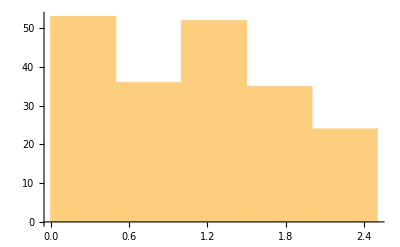

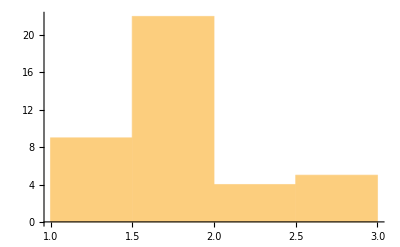

```mathematica
Histogram[trainingDataSmall//Values]
Histogram[validationDataSmall//Values]
```

```mathematica
Values[validationDataSmall]
```

{1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.87592,1.87592,1.87592,1.87592,2.27659,2.27659,2.27659,2.27659,2.55807,2.55807,2.55807,2.55807,2.68925}

```mathematica
Normal[trainingDataSmall][[1]]
```

File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/training/ODpBAi1TBVBvaW50wSMBAqa1VDPJUEBAY5~8smxZWMAtUwRab29tcvJvGxX1MkE~/ODpBAi1TBFpvb21yQpUkHJzuJj8tUwZOdW1iZXJDAg==.png]→0.209949

```mathematica
trainFeatures = MapAt[choppedTNet,Normal[trainingDataSmall],{All,1}];
validFeatures = MapAt[choppedTNet,Normal[validationDataSmall],{All,1}];
```

```mathematica
lastLayerTrain = NetTrain[finalLayers,trainFeatures,ValidationSet->validFeatures];
```

```mathematica
(*newTrainedNet = NetTrain[netJoin,Normal[trainingDataSmall],ValidationSet->Normal[validationDataSmall]];*)
```

```mathematica
lastLayerJoin = NetJoin[choppedTNet,lastLayerTrain]
ClearAll[testData]
testData = associateFilesToGeoRange[getFileNames["testing"]];
```

NetChain[<>]

### Examples:

```mathematica
testDataSmall[[1;;3]]
Map[Import,Take[Keys[testDataSmall],3]]
```

<|File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAi71~IKAaEBAHdiVA+JcWMAtUwRab29tcuWtsquqiHs~/ODpBAi1TBFpvb21ymB53chxbYj8tUwZOdW1iZXJDCQ==.png]→2.68885,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAi71~IKAaEBAHdiVA+JcWMAtUwRab29tcuWtsquqiHs~/ODpBAi1TBFpvb21ymB53chxbYj8tUwZOdW1iZXJDBA==.png]→2.68885,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAi71~IKAaEBAHdiVA+JcWMAtUwRab29tcuWtsquqiHs~/ODpBAi1TBFpvb21ymB53chxbYj8tUwZOdW1iZXJDBw==.png]→2.68885|>

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
lastLayerJoin[-Graphics-]
```

2.13191

```mathematica
Export[FileNameJoin[{"/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NeuralNets","amazonTrainedNet.wlnet"}],newTrainedNet];
```

### check error rate:

```mathematica
(Abs[newTrainedNet[trainingData[[All,1]]]-trainingData[[All,2]]])/trainingData[[All,2]]//Mean
```

1.73789

```mathematica
(Abs[newTrainedNet[testData[[All,1]]]-testData[[All,2]]])/testData[[All,2]]//Mean
```

1.31642

```mathematica
Abs[newTrainedNet[testData[[All,1]]]-testData[[All,2]]]//Mean
```

0.0635155